# Métodos Numéricos

## Toluca

## Actividad guiada

El clima de la ciudad de Toluca

La siguiente tabla muestra la temperatura promedio mensual (la alta y la baja) de la ciudad de Toluca durante dos años consecutivos (2011-2012).

```mathematica
Grid[{{2011,"Ene","Feb","Mar","Abr","May","Jun","Jul","Agos","Sept","Oct","Nov","Dic"},{"Alta",19,,,,,,,,,,,}},Frame->All]
```

2011 | Ene | Feb | Mar | Abr | May | Jun | Jul | Agos | Sept | Oct | Nov | Dic
Alta | 19 |  |  |  |  |  |  |  |  |  |  |

```mathematica
Grid[{{2011,"Ene","Feb","Mar","Abr","May","Jun","Jul","Agos","Sept","Oct","Nov","Dic"},{"Baja",2,,,,,,,,,,,}},Frame->All]
```

2011 | Ene | Feb | Mar | Abr | May | Jun | Jul | Agos | Sept | Oct | Nov | Dic
Baja | 2 |  |  |  |  |  |  |  |  |  |  |

## Busqueda de información

Para buscar la información solicitada en las tablas utilizaremos WolframAlpha (Se requiere una conexión a Internet)

```mathematica
WolframAlpha["Weather Toluca jan 2011",IncludePods->"WeatherSummary:WeatherData",AppearanceElements->{"Pods"},TimeConstraint->{30,Automatic,Automatic,Automatic}]
```

WolframAlphaQueryResults

## Busqueda de información (Observación)

Si requieres mayor información

Weather Toluca jan 2012

WolframAlphaQueryResults

## Generación de listas

Generar dos listas “baja” y “alta” (son 24 datos para cada lista)

```mathematica
baja={2,,,,,,,,,,,,,,,,,,,,,,,};
alta={19,,,,,,,,,,,,,,,,,,,,,,,};
```

## Generación de gráficas

Después de tener las listas podemos gráficar

```mathematica
ListPlot[{baja,alta}]
```

## Generacion de lista de datos para realizar un ajuste

```mathematica
tembaja=Table[{i,baja[[i]]},{i,1,Length[baja]}];
temalta=Table[{i,alta[[i]]},{i,1,Length[alta]}];
```

## Ajuste para la temperatura baja promedio

```mathematica
modelo=a Cos[b 2Pi x/12+c]+d;
regresion=FindFit[tembaja,modelo,{a,b,c,d},x]
```

## Ajuste para la temperatura alta promedio

```mathematica
modelo01=a Cos[b 2Pi x/12+c]+d;
regresion01=FindFit[temalta,modelo,{a,b,c,d},x]
```

## Evaluación y gráfica (Temperatura baja)

```mathematica
regresionf=Function[{},Evaluate[modelo/.regresion]];
Plot[regresionf[x],{x,1,24},PlotRange->{{1,24},{0,12}},Epilog->Map[Point,tembaja]]
```

## Evaluación y gráfica (Temperatura alta)

```mathematica
regresionf01=Function[{},Evaluate[modelo01/.regresion01]];
Plot[regresionf01[x],{x,1,24},PlotRange->{{1,24},{0,12}},Epilog->Map[Point,temalta]]
```

## Madrid Actividad I: Modelo de Temperaturas

Realiza lo anterior para la región de Madrid, España. Genera una predicción de la temperatura, la cual les permite a los hoteleros del lugar promoverse, presentando así las bondades del clima.

Grafica los datos. A partir de tu resultado, explica las características de la temperatura en Madrid.

Ajusta una función trigonométrica que se aproxime a los datos. La variable independiente debe ser el tiempo en meses. Para hacer esto, será necesario que encuentres la amplitud, el periodo de los datos y el momento en que ocurre el máximo (puedes tomar el modelo anterior).

Estima la temperatura que habrá los días 10 de Mayo, 16 de Septiembre y 25 de Diciembre.

### Introducción

El clima de la ciudad de Madrid

Las siguientes tablas muestran las temperaturas promedio mensuales (la alta y la baja) de la ciudad de Madrid durante dos años consecutivos (2012-2013).

2012 | Enero | Febrero | Marzo | Abril | Mayo | Junio | Julio | Agosto | Septiembre | Octubre | Noviembre | Diciembre
Baja | 1 | -1 | 5 | 6 | 13 | 18 | 19 | 20 | 15 | 10 | 7 | 3

2012 | Enero | Febrero | Marzo | Abril | Mayo | Junio | Julio | Agosto | Septiembre | Octubre | Noviembre | Diciembre
Alta | 12 | 12 | 17 | 15 | 25 | 30 | 33 | 33 | 27 | 20 | 13 | 10

2013 | Enero | Febrero | Marzo | Abril | Mayo | Junio | Julio | Agosto | Septiembre | Octubre | Noviembre | Diciembre
Baja | 3 | 3 | 5 | 7 | 9 | 14 | 20 | 20 | 16 | 12 | 5 | 2

2013 | Enero | Febrero | Marzo | Abril | Mayo | Junio | Julio | Agosto | Septiembre | Octubre | Noviembre | Diciembre
Alta | 10 | 11 | 13 | 17 | 21 | 29 | 35 | 34 | 30 | 22 | 15 | 12

## Búsqueda de Información

```mathematica
WolframAlpha["Weather Madrid dic 2012",IncludePods->"WeatherSummary:WeatherData",AppearanceElements->{"Pods"},TimeConstraint->{30,Automatic,Automatic,Automatic}]
```

WolframAlphaQueryResults

## Búsqueda de Información (Extra)

Weather Madrid jan 2012

WolframAlphaQueryResults

## Generación de Listas

Generar dos listas, “baja” y “alta” (son 24 datos para cada lista)-

```mathematica
baja={1,-1,5,6,13,18,19,20,15,10,7,3,3,3,5,7,9,14,20,20,16,12,5,2};
alta={12,12,17,15,25,30,33,33,27,20,13,10,10,11,13,17,21,29,35,34,30,22,15,12};
```

## Generación de Gráficas

Después de tener las listas podemos gráficar

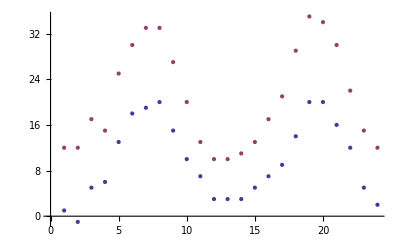

```mathematica
ListPlot[{baja,alta}]
```

## Generacion de listas de datos para realizar un ajuste

```mathematica
temBaja=Table[{i,baja[[i]]},{i,1,Length[baja]}];
temAlta=Table[{i,alta[[i]]},{i,1,Length[alta]}];
```

## Ajuste para la temperatura baja promedio

```mathematica
modelo=a Cos[b 2Pi x/12+c]+d;
regresion=FindFit[temBaja,modelo,{a,b,c,d,a2,b2,c2,d2},x]
```

{a→9.12968,b→0.997271,c→8.6988,d→9.64428,a2→1.,b2→1.,c2→1.,d2→1.}

## Ajuste para la temperatura alta promedio

```mathematica
modelo01=a1 Cos[b1 2Pi x/24+c1]+d1;
regresion01=FindFit[temAlta,modelo01,{a1,b1,c1,d1},x]
```

{a1→-11.7708,b1→1.9696,c1→-0.56504,d1→20.4979}

## Evaluación y Gráfica (Temperatura Baja)

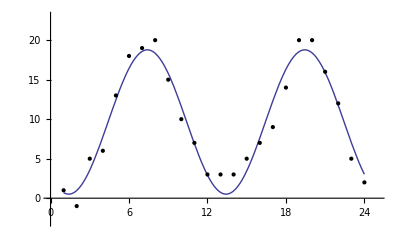

```mathematica
regresionf=Function[{},Evaluate[modelo/.regresion]];
Plot[regresionf[x],{x,1,24},PlotRange->{{0,25},{-3,23}},Epilog->Map[Point,temBaja]]
```

## Evaluación y Gráfica (Temperatura Alta)

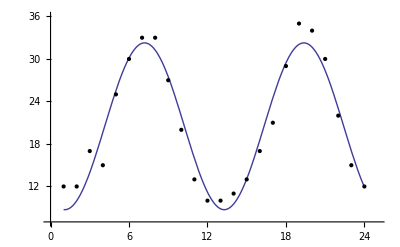

```mathematica
regresionf01=Function[{},Evaluate[modelo01/.regresion01]];
Plot[regresionf01[x],{x,1,24},PlotRange->{{0,25},{7,36}},Epilog->Map[Point,temAlta]]
```

## Expliación de la Temperatura en Madrid

La temperatura de Madrid se asemeja a la que existe en Toluca, sin embargo, en Madrid no hay disimilitudes exageradas, diariamente, en cuanto a grados. A diferencia de Toluca, en Madrid hay pocos días de lluvia, de neblina y de tormenta.
El comportamiento anual, como habría de esperarse, resulta ser una distribución normal. Esto se debe a las estaciones del año, ya que éste comienza con un frío Invierno, alcanza altas temperaturas en Verano, y a su término, todo se vuelve a congelar. Podemos concluir que en la capital hispana continúan existiendo, de forma debida, las épocas anuales.

## Estimaciones de Temperaturas

Para estimar las temperaturas que habrá el 10 de Mayo, el 16 de Semptiembre y el 25 de Diciembre, se utilizarán las temperaturas “bajas” y “altas” que han habido en esos días, durante los últimos 4 años. Se generará una temperatura media (esperanza) a partir del arreglo generado.

```mathematica
diaMadresBaja={13,15,15,9};
diaMadresAlta={24,30,26,17};
```

```mathematica
diaMadresEstimado={13,24};
```

```mathematica
diaIndependenciaBaja={16,16,20,18};
diaIndependenciaAlta={31,33,31,26};
```

```mathematica
diaIndependenciaEstimado={18,30};
```

```mathematica
diaNavidadBaja={1,5,3,0};
diaNavidadAlta={15,11,9,10};
```

```mathematica
diaNavidadEstimado={2,11};
```

```mathematica
{{, "10 de Mayo", "16 de Septiembre", "25 de Diciembre"}, {"Baja", 13, 18, 2}, {"Alta", 24, 30, 11}}
```

```mathematica
WolframAlpha["Weather Madrid dic 25 2013",IncludePods->"WeatherSummary:WeatherData",AppearanceElements->{"Pods"},TimeConstraint->{30,Automatic,Automatic,Automatic}]
```

WolframAlphaQueryResults

## Actividad II: Calcular el volúmen de una “Coca-Cola”

Foto de una “Coca-Cola "

Tomar puntos sobre el perfil

Graficar el perfil (dispersión)

Generar el modelo con “FindFit”

Producir la función p[x] y graficar “Plot[{p[x],-p[x]},{x,0,25},AspectRatio→Automatic]”

Crear el sólido de revolución

Usar Trapecio y Riemann para calcular el volúmen de la “Coca Cola”  ( f[x_]:=Pi*(p[x])^2 )

Foto de una “Coca-Cola”

```mathematica
Import["http://neetcurioso.com/wp-content/uploads/2013/02/coca-cola-noticia.jpg"]
```

Tomar puntos sobre el perfil

```mathematica
datos = {{2426.44,962.897},{2422.95,1088.58},{2395.02,1189.83},{2367.09,1252.67},{2325.2,1294.57},{2262.35,1308.53},{2178.56,1315.52},{2126.19,1315.52},{2059.86,1305.04},{1983.05,1277.11},{1930.68,1266.64},{1871.33,1263.15},{1793.39,1271.73},{1681.1,1287.77},{1597.69,1299.},{1531.92,1308.63},{1487.,1310.23},{1416.42,1310.23},{1312.16,1308.63},{1203.08,1300.61},{1097.21,1282.96},{1018.61,1270.13},{949.63,1255.69},{895.09,1239.65},{818.093,1218.8},{726.659,1185.11},{606.351,1146.61},{519.73,1125.76},{415.463,1112.93},{356.111,1108.12},{324.029,1106.51},{295.155,1127.36},{258.261,1114.53},{229.387,1106.51},{200.513,1127.36},{166.827,1119.34},{147.578,1076.03},{134.745,982.995}};
```

Graficar el perfil (dispersión)

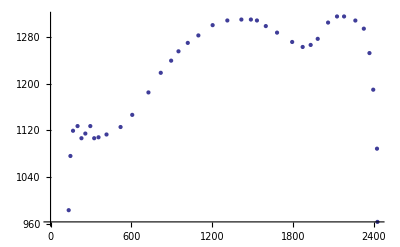

```mathematica
ListPlot[datos]
```

Generar el modelo con “FindFit”

```mathematica
Clear[a,b,c,d,a2,b2,c2,d2,e,f,i,j,k,l,m,n,o,p,q,r]
```

```mathematica
modeloCoca= a x^3+b x^2+c x +d+a2 x^4+b2 x^5+c2 x^6+d2 x^7+e x^8+f x^9+i x^10+j x^11+k x^12+l x^13+m x^14+n x^15+o x^16+p x^17+q x^18+r x^19;
regresionCoca=FindFit[datos,modeloCoca,{a,b,c,d,a2,b2,c2,d2,e,f,i,j,k,l,m,n,o,p,q,r},x]
```

{a→0.0680884,b→-9.5364,c→783.439,d→-27265.2,a2→-0.000319951,b2→1.05211×10^-6,c2→-2.51108×10^-9,d2→4.44568×10^-12,e→-5.9011×10^-15,f→5.87×10^-18,i→-4.30469×10^-21,j→2.21344×10^-24,k→-6.72985×10^-28,l→1.17175×10^-33,m→1.16458×10^-34,n→-6.4813×10^-38,o→1.97536×10^-41,p→-3.6874×10^-45,q→3.97297×10^-49,r→-1.90624×10^-53}

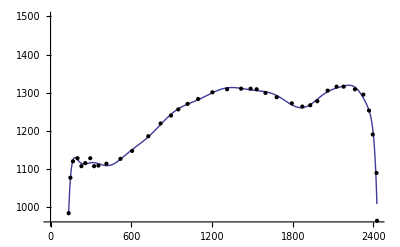

```mathematica
regresionfCoca=Function[{},Evaluate[modeloCoca/.regresionCoca]];
Plot[regresionfCoca[x],{x,134,2426},PlotRange->{{0,2430},{960,1500}},Epilog->Map[Point,datos]]
```

Producir la función p[x] y graficar “Plot[{p[x],-p[x]},{x,0,25},AspectRatio→Automatic]”

```mathematica
vol[y_]:=regresionfCoca[[2]]/.x->y
```

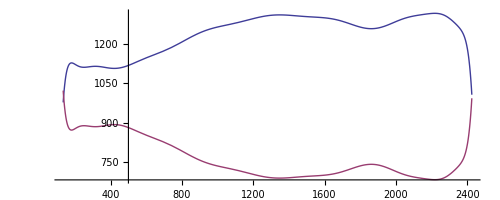

```mathematica
Plot[{vol[x],-vol[x]+2000},{x,134,2426},AspectRatio->Automatic]
```

```mathematica
(** Se ajusta la función en el origen **)
```

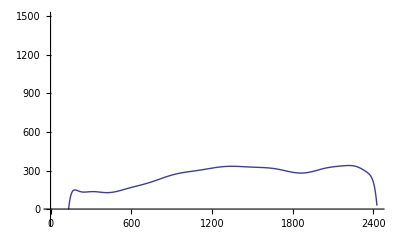

```mathematica
Plot[{vol[y]-980},{y,134,2426},PlotRange->{{0,2430},{-100,1500}}]
```

```mathematica
funcion[x_]:=vol[y]-980 /.y->x
```

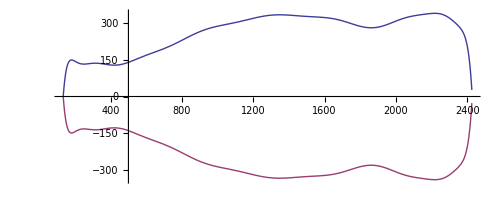

```mathematica
Plot[{funcion[x],-funcion[x]},{x,134,2426},AspectRatio->Automatic]
```

Crear sólido de revolución

```mathematica
RevolutionPlot3D[{funcion[x],x },{x,134,2426},{θ,-Pi,Pi},Mesh-> False,Boxed->False,Axes->True, Background-> White,PerformanceGoal->"Quality", PlotStyle-> Directive[Black, Specularity[Red, 20]]]
```

-Graphics3D-

Usar Trapecio y Riemann para calcular el volúmen de la “Coca Cola”  ( f[x_]:=Pi*(p[x])^2 )

```mathematica
z[x_]:=Pi*(funcion[x])^2
```

```mathematica
metodoTrapecio[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n-1,i++,
sum =sum+z[a+i*h];];
Return[h/2(z[a]+z[b])+h*sum];
];
```

```mathematica
sumaInferiorRiemann[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=0,i≤ n-1,i++,
sum =sum+h*z[a+i*h];];
Return[sum];
];
```

```mathematica
sumaSuperiorRiemann[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n,i++,
sum =sum+h*z[a+i*h];];
Return[sum];
];
```

```mathematica
metodoTrapecio[134,2426,50]
```

5.27286×10^8

```mathematica
sumaInferiorRiemann[134,2426,50]
```

5.27235×10^8

```mathematica
sumaSuperiorRiemann[134,2426,50]
```

5.27337×10^8

```mathematica
(** NOTA: Las unidades son pixeles^3 **)
```